```mathematica
Integrate[1/7*(1-Exp[-3(7-x)]),{x,0,7}]
```

1/21 (20+1/ⅇ^21)

```mathematica
Integrate[1/F*(1-Exp[-l*(Floor[(k+x)/F]*F-x)]),{x,0,F}]
```

∫_0^F (1-ⅇ^(-l (-x+F Floor[(k+x)/F])))/F ⅆx

```mathematica
(-1+ⅇ^(-k T)+k T)/(k T)
```

(-1+ⅇ^(-k T)+k T)/(k T)

```mathematica
Together[(-1+ⅇ^(-k T)+k T)/(k T)]
```

(ⅇ^(-10 T) (1-ⅇ^(10 T)+10 ⅇ^(10 T) T))/(10 T)

```mathematica
f=15
l=0.1
k=20
```

15

0.1

20

```mathematica
g[x_]:=Piecewise[{{1-Exp[-l*x] ,x>=0},{0,x<0}}]
```

```mathematica
pk = Integrate[1/f*g[Floor[(k+x)/f]*f-x],{x,0,f}]
```

∫_0^15 1/15 (1-ⅇ^(-0.1 (-x+15 Floor[(k+x)/15])))ⅆx

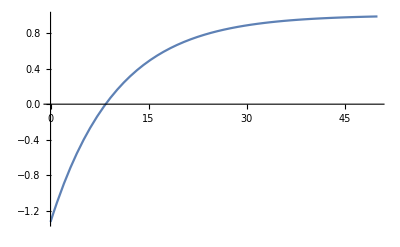

```mathematica
Plot[pk,{k,0,50}]
```